# Амплитудная модуляция на пальцах

В недавней статье “Амплитудная модуляция произвольного сигнала”  её автор довольно сумбурно попытался представить своё понимание формирования спектра при амплитудной модуляции. Но отсутствие иллюстраций и избыток математики с привлечением интегральных преобразований помешало сообществу понять мысли автора и оценить статью по достоинству; в то время как тема это достаточно простая - рассмотреть которую мы и попробуем ещё раз с привлечением Wolfram Mathematica.

Итак, идея  амплитудной модуляции  состоит в том, чтобы передавать низкочастотный сигнал - голос или музыку - модулируя высокочастотный (несущий) сигнал, многократно превышающий слышимый диапазон и занимающий узкую полосу частот в радиоэфире. Сама модуляция осуществляется простым умножением сигнала на несущий:

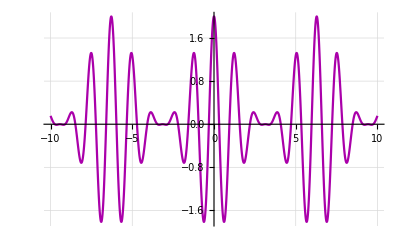

```mathematica
Plot[Cos[5x]*(Cos[x]+1),{x,-10,10},GridLines->Automatic,PlotStyle->{Magenta//Darker}]
```

Здесь у нас в качестве несущей выступает синусоида с частотой 5:

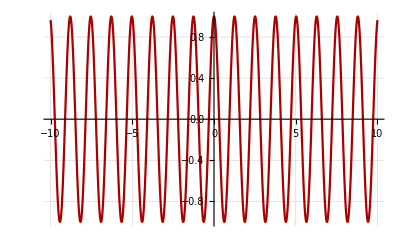

```mathematica
Plot[Cos[5x],{x,-10,10},GridLines->Automatic,PlotStyle->{Red//Darker}]
```

А сам сигнал - с частотой 1:

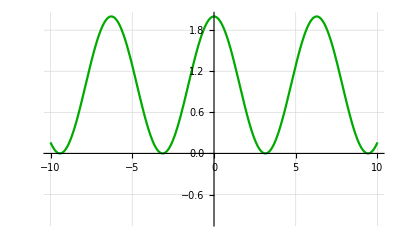

```mathematica
Plot[Cos[x]+1,{x,-10,10},PlotRange->{-1,2},GridLines->Automatic,PlotStyle->{Green//Darker}]
```

Можно заметить, что сигнал смещён вверх и имеет только положительные значения. Это не случайно и является обязательным условием для возможности последующего его корректного восстановления. Как же его восстановить? Очень просто! Нужно сдвинуть фазу сигнала на 90 градусов (операция, известная как преобразование Гильберта, и посчитать корень из суммы квадратов модулированного и преобразованного сигналов:

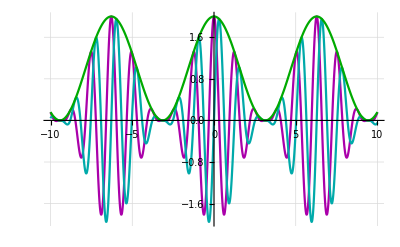

```mathematica
Plot[{
Cos[5x]*(Cos[x]+1),
Sin[5x]*(Cos[x]+1),
√((Cos[5x]*(Cos[x]+1))^2+(Sin[5x]*(Cos[x]+1))^2)
},{x,-10,10},GridLines->Automatic,PlotStyle->{Magenta//Darker,Cyan//Darker,Green//Darker}]
```

В более простом (но грубом) варианте преобразование Гильберта можно заменить задержкой сигнала на четверть периода несущий частоты, а итоговый сигнал дополнительно отфильтровать фильтром низких частот. В ещё более простом варианте можно вообще не считать корней и квадратов, а отфильтровать сигнал по абсолютному значению (что и применяется обычно в радиоприёмниках).

Теперь посмотрим, что у нас происходит со спектрами. Посчитаем преобразование Фурье от несущего сигнала:

```mathematica
FourierTransform[Cos[5x],x,w]
```

√(π/2) DiracDelta[-5+w]+√(π/2) DiracDelta[5+w]

Так как дельта-функция Дирака не является функцией в классическом смысле, её график нельзя построить стандартным способом; поэтому сделаем это вручную, используя общепринятое начертание:

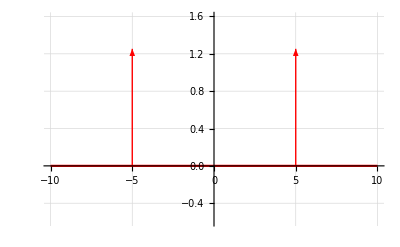

```mathematica
Plot[0,{f,-10,10},PlotRange->{-0.6,1.6},GridLines->Automatic,PlotStyle->{Red},
Epilog->{Red,Arrow[{{{-5,0},{-5,√(π/2)}},{{5,0},{5,√(π/2)}}}]}]
```

Ожидаемо получили ту же частоту, что и в начальной формуле. Наличие ещё одной такой же частоты не случайно - это явление называется Hermitian symmetry и является следствием того, что рассматриваемая функция сугубо действительная и в комплексном представлении имеет нулевую мнимую компоненту. Отсутствие мнимых компонент в спектре после преобразования обусловлено тем, что изначально наши функции ещё и чётные (симметричные относительно нуля).

Теперь сделаем преобразование Фурье для самого сигнала:

```mathematica
FourierTransform[Cos[x]+1,x,w]
```

√(π/2) DiracDelta[-1+w]+√(2 π) DiracDelta[w]+√(π/2) DiracDelta[1+w]

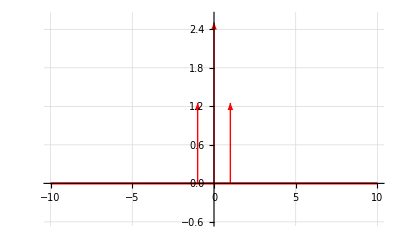

```mathematica
Plot[0,{f,-10,10},PlotRange->{-0.6,2.6},GridLines->Automatic,PlotStyle->{Red},
Epilog->{Red,Arrow[{{{-1,0},{-1,√(π/2)}},{{0,0},{0,√(2 π)}},{{1,0},{1,√(π/2)}}}]}]
```

Здесь мы дополнительно получили дельта-функцию Дирака в центре координат — вследствие наличия в сигнале постоянной составляющей, которая не имеет колебаний по определению — что позволяет её рассматривать как нулевую частоту.

Что же будет со спектром, если их перемножить? Посмотрим:

```mathematica
FourierTransform[Cos[5x](Cos[x]+1),x,w]
```

1/2 √(π/2) DiracDelta[-6+w]+√(π/2) DiracDelta[-5+w]+1/2 √(π/2) DiracDelta[-4+w]+1/2 √(π/2) DiracDelta[4+w]+√(π/2) DiracDelta[5+w]+1/2 √(π/2) DiracDelta[6+w]

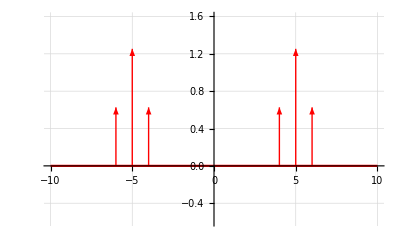

```mathematica
Plot[0,{f,-10,10},PlotRange->{-0.6,1.6},GridLines->Automatic,PlotStyle->{Red},
Epilog->{Red,Arrow[{{{-6,0},{-6,√(π/8)}},{{-5,0},{-5,√(π/2)}},{{-4,0},{-4,√(π/8)}},
{{4,0},{4,√(π/8)}},{{5,0},{5,√(π/2)}},{{6,0},{6,√(π/8)}}}]}]
```

Из теории мы знаем, что умножение во временном домене равносильно свертке в частотном (и наоборот, что широко используется при FIR-фильтрации). А поскольку один из подвергаемых свёртке сигналов состоял только из одной (положительной и отрицательной) частоты, то в результате свёртки мы получили просто перенос сигнала вверх по частоте. И так как симметрия осталась, сигнал у нас по-прежнему не имеет мнимой компоненты.

Приведём его теперь к комплексному (аналитическому) виду, обнулив отрицательную область частот:

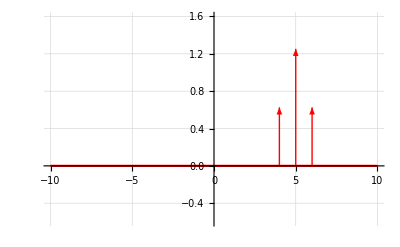

```mathematica
Plot[0,{f,-10,10},PlotRange->{-0.6,1.6},GridLines->Automatic,PlotStyle->{Red},
Epilog->{Red,Arrow[{{{4,0},{4,√(π/8)}},{{5,0},{5,√(π/2)}},{{6,0},{6,√(π/8)}}}]}]
```

и сделаем обратное преобразование Фурье:

```mathematica
InverseFourierTransform[1/2 √(π/2) DiracDelta[4+w]+√(π/2) DiracDelta[5+w]+1/2 √(π/2) DiracDelta[6+w],w,x]
```

1/4 ⅇ^(4 ⅈ x) (1+ⅇ^(ⅈ x))^2

Так как функция комплексная, для построения её графика необходимо отдельно извлечь действительную и мнимую компоненты:

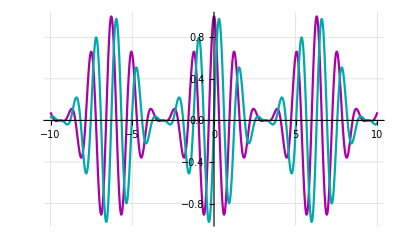

```mathematica
Plot[{
1/4 ⅇ^(4 ⅈ x) (1+ⅇ^(ⅈ x))^2//Re,
1/4 ⅇ^(4 ⅈ x) (1+ⅇ^(ⅈ x))^2//Im
},{x,-10,10},GridLines->Automatic,PlotStyle->{Magenta//Darker,Cyan//Darker,Green//Darker}]
```

Теперь у нашего сигнала появилась мнимая компонента, представляющая собой сдвинутый  на 90 градусов исходный сигнал. Это будет более очевидно, если представить полученную функцию в тригонометрическом виде:

```mathematica
1/4 ⅇ^(4 ⅈ x) (1+ⅇ^(ⅈ x))^2//ExpToTrig
```

1/4 (1+Cos[x]+ⅈ Sin[x])^2 (Cos[4 x]+ⅈ Sin[4 x])

Пока не очень очевидно. Попробуем упростить:

```mathematica
1/4 (1+Cos[x]+ⅈ Sin[x])^2 (Cos[4 x]+ⅈ Sin[4 x])//Simplify
```

Cos[x/2]^2 (Cos[5 x]+ⅈ Sin[5 x])

Теперь больше похоже на правду - и как видим, функция нашего исходного сигнала тоже упростилась. Попробуем её вернуть к оригинальному виду:

```mathematica
Cos[x/2]^2//TrigReduce
```

1/2 (1+Cos[x])

Множитель 1/2 появился не случайно - ведь обнулив половину спектра, мы соответственно и уменьшили мощность сигнала. Ну а теперь, имея модулированный комплексный сигнал, мы можем взять и этот модуль посчитать:

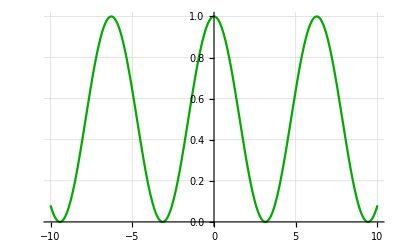

```mathematica
Plot[{
Cos[x/2]^2 (Cos[5 x]-ⅈ Sin[5 x])//Abs
},{x,-10,10},GridLines->Automatic,PlotStyle->{Magenta//Darker,Cyan//Darker,Green//Darker}]
```

Модуль комплексного числа как раз и считается через корень суммы квадратов мнимого и действительных компонентов. И отсюда понятно, почему кодируемый сигнал должен состоять только из положительных значений - если он будет включать отрицательные значения, то после восстановления они также станут положительными, что и называется перемодуляцией:

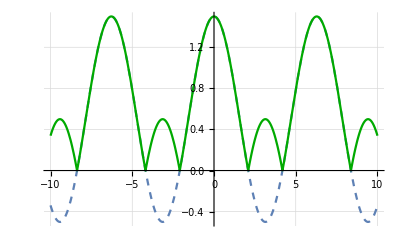

```mathematica
Plot[{
(1/2+Cos[x]),
(1/2+Cos[x])(Cos[5 x]-ⅈ Sin[5 x])//Abs
},{x,-10,10},GridLines->Automatic,PlotStyle->{Dashed,Green//Darker}]
```

Восстановление сигнала также возможно и при помощи квадратурного гетеродина - когда модулированный сигнал снова умножается на несущую частоту, но на этот раз - комплексную:

```mathematica
FourierTransform[(Cos[5 x]+I Sin[5 x]),x,w]
```

√(2 π) DiracDelta[5+w]

```mathematica
FourierTransform[(1+Cos[x])Cos[5 x]*(Cos[5 x]+I Sin[5 x]),x,w]
```

1/2 √(π/2) DiracDelta[-1+w]+√(π/2) DiracDelta[w]+1/2 √(π/2) DiracDelta[1+w]+1/2 √(π/2) DiracDelta[9+w]+√(π/2) DiracDelta[10+w]+1/2 √(π/2) DiracDelta[11+w]

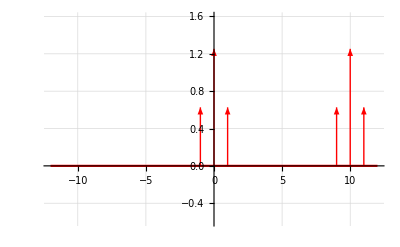

```mathematica
Plot[0,{f,-12,12},PlotRange->{-0.6,1.6},GridLines->Automatic,PlotStyle->{Red},
Epilog->{Red,Arrow[{{{-1,0},{-1,√(π/8)}},{{0,0},{0,√(π/2)}},{{1,0},{1,√(π/8)}},
{{9,0},{9,√(π/8)}},{{10,0},{10,√(π/2)}},{{11,0},{11,√(π/8)}}}]}]
```

За счёт того, что комплексная частота в частотной области имеет только один импульс без дублирования его в отрицательной области частот - то в результате свёртки мы получим линейный перенос спектра, при которой отрицательная часть спектра встанет обратно в центр, а положительная - сдвинется ещё дальше, и её останется только отфильтровать фильтром нижних частот.

## Заключение

Как видим, в рассмотрении амплитудной модуляции через преобразовании Фурье нет ничего сложного; если же рассматривать её исключительно на школьном уровне, то достаточно вспомнить, что произведение (несущей) суммы (представление сигнала в виде тригонометрического ряда) равнозначно сумме произведений (каждого члена ряда по отдельности на несущую частоту) - и, соответственно, каждое такое произведение раскладывается в сумму двух синусоид по уже озвученной формуле.

Внимательный читатель также мог заметить, что раз в результате модуляции мы получили симметричный спектр - значит, имеет место быть избыточность данных и можно оставить только одну боковую полосу, сократив тем самым занимаемую полосу частот в радиоэфире. Такая технология действительно имеется, но это - уже совсем другая история.